# Code

```mathematica
file = "../results/res11p2-target-180";
```

```mathematica
importResults[file]
```

```mathematica
restest = {"An-t1-l0"->{23477,24950,36828,1035,52504,1282,51737,5653,11417,17346},"Ao-t1-l0"->{49714,17484,15319,1523,19363,1870,1868,29880,15158,3325},"Ap-t1-l0"->{6542,5116,48023,2895,16766,2388,36734,10067,17326,6573},"Bn-t1-l1"->{14756,12328,18538,8693,15403,6191,3385,14536,23995,8072},"Bo-t1-l1"->{29143,23658,38837,8694,29737,53476,16298,22633,3754,5657},"Bp-t1-l1"->{27955,23665,24978,8751,26435,41387,27245,5844,9108,13776}}
```

{An-t1-l0→{23477,24950,36828,1035,52504,1282,51737,5653,11417,17346},Ao-t1-l0→{49714,17484,15319,1523,19363,1870,1868,29880,15158,3325},Ap-t1-l0→{6542,5116,48023,2895,16766,2388,36734,10067,17326,6573},Bn-t1-l1→{14756,12328,18538,8693,15403,6191,3385,14536,23995,8072},Bo-t1-l1→{29143,23658,38837,8694,29737,53476,16298,22633,3754,5657},Bp-t1-l1→{27955,23665,24978,8751,26435,41387,27245,5844,9108,13776}}

```mathematica
parseDirName["Bp-t1-l0"]
```

{Bp,1,0}

```mathematica
reorderRules[restest]
```

{An-t1-l0→{23477,24950,36828,1035,52504,1282,51737,5653,11417,17346},Ap-t1-l0→{6542,5116,48023,2895,16766,2388,36734,10067,17326,6573},Ao-t1-l0→{49714,17484,15319,1523,19363,1870,1868,29880,15158,3325},Bn-t1-l1→{14756,12328,18538,8693,15403,6191,3385,14536,23995,8072},Bp-t1-l1→{27955,23665,24978,8751,26435,41387,27245,5844,9108,13776},Bo-t1-l1→{29143,23658,38837,8694,29737,53476,16298,22633,3754,5657}}

```mathematica
reorderResults[restest]
```

{{An-t1-l0→{23477,24950,36828,1035,52504,1282,51737,5653,11417,17346},Ap-t1-l0→{6542,5116,48023,2895,16766,2388,36734,10067,17326,6573},Ao-t1-l0→{49714,17484,15319,1523,19363,1870,1868,29880,15158,3325}},{Bn-t1-l1→{14756,12328,18538,8693,15403,6191,3385,14536,23995,8072},Bp-t1-l1→{27955,23665,24978,8751,26435,41387,27245,5844,9108,13776},Bo-t1-l1→{29143,23658,38837,8694,29737,53476,16298,22633,3754,5657}}}

```mathematica
20 * 60
```

1200

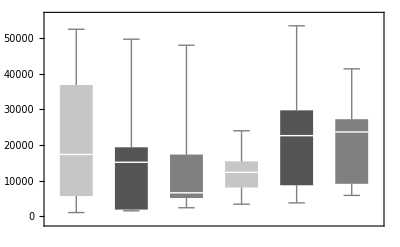
-Graphics--Graphics- | An-t1-l0
-Graphics- | Ao-t1-l0
-Graphics- | Ap-t1-l0
-Graphics- | Bn-t1-l0
-Graphics- | Bo-t1-l0
-Graphics- | Bp-t1-l0

```mathematica
boxChartOfResults[file]
```

```mathematica
res2 = importResults["../results/res2"];
```

```mathematica
"An-t1-l0" /. res2
```

{18521,8407,5676,428,30750,27739,12113,24747,6493,41204,15982,22249,4995,5717,52840,28573,29058,23238,3308,11564,53140,21519,19837,2602,5513,32958,279,736,6140,2337,11416,33612,1378,9337}

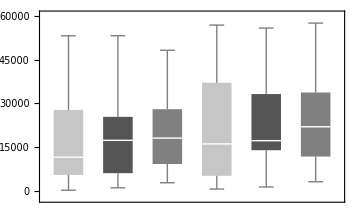
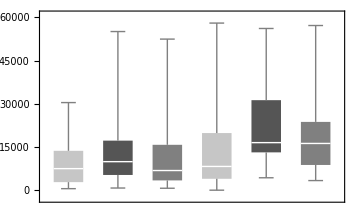
-Graphics--Graphics- | An-t1-l0
-Graphics- | Ap-t1-l0
-Graphics- | Ao-t1-l0
-Graphics- | Bn-t1-l0
-Graphics- | Bp-t1-l0
-Graphics- | Bo-t1-l0
-Graphics--Graphics- | An-t1-l1
-Graphics- | Ap-t1-l1
-Graphics- | Ao-t1-l1
-Graphics- | Bn-t1-l1
-Graphics- | Bp-t1-l1
-Graphics- | Bo-t1-l1

```mathematica
Column[Map[boxChartOfResults, reorderResults[res2]]]
```

```mathematica
chartLabelsHelper[keys[restest]]
```

{,,A,,,B}

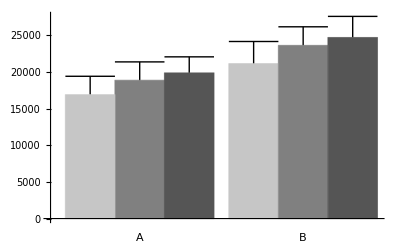
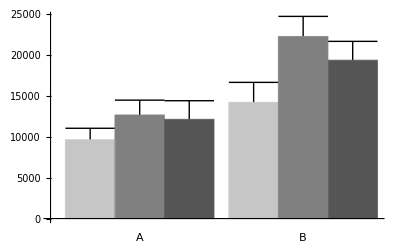
-Graphics--Graphics- | n
-Graphics- | p
-Graphics- | o
-Graphics--Graphics- | n
-Graphics- | p
-Graphics- | o

```mathematica
Column[Map[chartOfResults, reorderResults[res2]]]
```

# Read Results

```mathematica
<<loadall`
```

```mathematica
loadall[];
```

```mathematica
link = Install["run-simulation-mlink"];
```

```mathematica
Uninstall[link]
```

/Users/shane/School/sussex/thesis/code/src/run-simulation-mlink

```mathematica
Clear[runSimulationMlink]
```

```mathematica
restest
```

```mathematica
chartOfResults[restest]
```

```mathematica
MannWhitneyTest[{%117[[1]], %117[[3]]}]
```

0.384673

```mathematica
maxEvalsOfResults[res_] := mapValues[ #[[All,-1,-1]]&,res]
```

```mathematica
evalsForPhasesOfResults[res_] := mapValues[ #[[All,All,-1]]&,res]
```

```mathematica
mapValues[fn_, rules_] := rules /. Rule[k_, v_] :> Rule[k, fn[v]]
```

```mathematica
byRow[fn_, matrix_] := Transpose[fn[Transpose[matrix]]]
```

```mathematica
Mean[{1783,2713,4039,5006}] //N
```

3385.25

```mathematica
evalsForPhasesOfResults[res]
```

{An-t1-l0→{{6108},{3192},{4689},{3359},{6267},{5917},{10379},{3092},{3993},{25224}},Ao-t1-l0→{{1783,2713,4039,5006},{2577,3151,3377,7674},{983,3212,7821,16031},{1991,2989,7183,15945},{2404,2983,5698,7606},{2077,3398,6209,11476},{1505,2078,2661,5172},{2981,7520,10169,11005},{2539,4761,16248,25516},{1496,2282,4526,6430}},Ap-t1-l0→{{701,2877,5345,5673},{1551,4186,6431,6777},{1921,4214,9075,25636},{1538,4702,5938,7952},{1224,5039,25601,25751},{405,1916,7435,7588},{807,2894,7088,13452},{861,1224,2407,2698},{1593,4573,10761,13796},{767,2259,7723,11586}},Bn-t1-l0→{{4458},{8579},{4710},{5101},{11292},{4812},{5495},{19491},{14847},{8683}},Bo-t1-l0→{{3143,5381,10440,25382},{2973,4632,5829,8622},{1955,3066,4295,19943},{2212,3294,21554,25356},{1469,2912,7314,11124},{3995,4826,25371,25521},{2184,6138,14970,23580},{3408,4321,25247,25397},{483,1089,4643,8826},{2197,9637,25197,25347}},Bp-t1-l0→{{1008,4214,9311,9461},{957,2690,7346,7886},{1602,11347,25462,25612},{534,1914,25561,25711},{1303,4139,12155,14786},{1815,6216,9854,11692},{1427,3781,25019,25169},{695,4131,8524,9075},{1715,3979,25521,25671},{649,4622,23190,24286}}}

```mathematica
mapValues[N[Mean[#]]&,%228]
```

{An-t1-l0→{7222.},Ao-t1-l0→{2033.6,3508.7,6793.1,11186.1},Ap-t1-l0→{1136.8,3388.4,8780.4,12090.9},Bn-t1-l0→{8746.8},Bo-t1-l0→{2401.9,4529.6,14486.,19909.8},Bp-t1-l0→{1170.5,4703.3,17194.3,17934.9}}

```mathematica
values[%241]
```

{{7222.},{2033.6,3508.7,6793.1,11186.1},{1136.8,3388.4,8780.4,12090.9},{8746.8},{2401.9,4529.6,14486.,19909.8},{1170.5,4703.3,17194.3,17934.9}}

```mathematica
res = importResults["../results/al1"];
```

```mathematica
values[res]
```

{{6108,3192,4689,3359,6267,5917,10379,3092,3993,25224},{5006,7674,16031,15945,7606,11476,5172,11005,25516,6430},{5673,6777,25636,7952,25751,7588,13452,2698,13796,11586},{4458,8579,4710,5101,11292,4812,5495,19491,14847,8683},{25382,8622,19943,25356,11124,25521,23580,25397,8826,25347},{9461,7886,25612,25711,14786,11692,25169,9075,25671,24286}}

```mathematica
%67
```

{An-t1-l0→{6108,3192,4689,3359,6267,5917,10379,3092,3993,25224},Ap-t1-l0→{5673,6777,25636,7952,25751,7588,13452,2698,13796,11586},Ao-t1-l0→{5006,7674,16031,15945,7606,11476,5172,11005,25516,6430},Bn-t1-l0→{4458,8579,4710,5101,11292,4812,5495,19491,14847,8683},Bp-t1-l0→{9461,7886,25612,25711,14786,11692,25169,9075,25671,24286},Bo-t1-l0→{25382,8622,19943,25356,11124,25521,23580,25397,8826,25347}}

```mathematica
%67
```

{An-t1-l0→{6108,3192,4689,3359,6267,5917,10379,3092,3993,25224},Ap-t1-l0→{5673,6777,25636,7952,25751,7588,13452,2698,13796,11586},Ao-t1-l0→{5006,7674,16031,15945,7606,11476,5172,11005,25516,6430},Bn-t1-l0→{4458,8579,4710,5101,11292,4812,5495,19491,14847,8683},Bp-t1-l0→{9461,7886,25612,25711,14786,11692,25169,9075,25671,24286},Bo-t1-l0→{25382,8622,19943,25356,11124,25521,23580,25397,8826,25347}}

```mathematica
res
```

{An-t1-l0→{6108,3192,4689,3359,6267,5917,10379,3092,3993,25224},Ao-t1-l0→{5006,7674,16031,15945,7606,11476,5172,11005,25516,6430},Ap-t1-l0→{5673,6777,25636,7952,25751,7588,13452,2698,13796,11586},Bn-t1-l0→{4458,8579,4710,5101,11292,4812,5495,19491,14847,8683},Bo-t1-l0→{25382,8622,19943,25356,11124,25521,23580,25397,8826,25347},Bp-t1-l0→{9461,7886,25612,25711,14786,11692,25169,9075,25671,24286}}

```mathematica
reorderResults[res]
```

{{An-t1-l0→{6108,3192,4689,3359,6267,5917,10379,3092,3993,25224},Ap-t1-l0→{5673,6777,25636,7952,25751,7588,13452,2698,13796,11586},Ao-t1-l0→{5006,7674,16031,15945,7606,11476,5172,11005,25516,6430},Bn-t1-l0→{4458,8579,4710,5101,11292,4812,5495,19491,14847,8683},Bp-t1-l0→{9461,7886,25612,25711,14786,11692,25169,9075,25671,24286},Bo-t1-l0→{25382,8622,19943,25356,11124,25521,23580,25397,8826,25347}}}

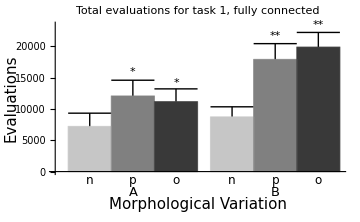
-Graphics--Graphics- | No morphological change
-Graphics- | Phylogenetic change
-Graphics- | Ontogenetic change

```mathematica
chartOfResults[res]
```

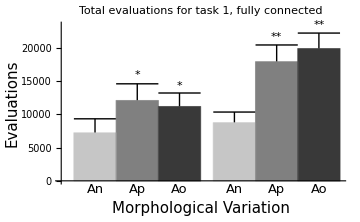
-Graphics--Graphics- | No morphological change
-Graphics- | Phylogenetic change
-Graphics- | Ontogenetic change

```mathematica
chartOfResults[res]
```

```mathematica
Export["../doc/fig/evals-t1-l0.pdf", %]
```

../doc/fig/evals-t1-l0.pdf

```mathematica
Scaled[{1,1}]
```

Scaled[{1,1}]

```mathematica
?Scaled
```

Scaled[{x,y,…}] gives the position of a graphical object in terms of coordinates scaled to run from 0 to 1 across the whole plot range in each direction. 
Scaled[{dx,dy,…},{x_0,y_0,…}] gives a position obtained by starting at ordinary coordinates {x_0,y_0,…}, then moving by a scaled offset {dx,dy,…}.

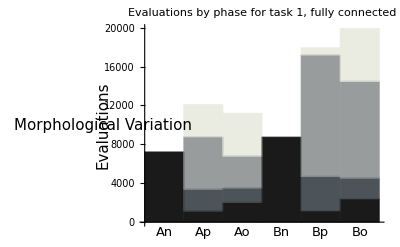
-Graphics--Graphics- | p1
-Graphics- | p2
-Graphics- | p3
-Graphics- | p4

```mathematica
chartStepsOfResults[res]
```

```mathematica
Export["step-evals.pdf", %328]
```

step-evals.pdf

```mathematica
titlePlot[%67]
```

Plot of task 1, fully connected

```mathematica
parseDirName["An-t1-l0"]
```

{An,1,0,A,n}

```mathematica
{1783,2713,4039,5006}
```

{1783,2713,4039,5006}

```mathematica
RotateRight[%]
```

{5006,1783,2713,4039}

```mathematica
%265 - %266
```

{-3223,930,1326,967}

```mathematica
cumulativeToNon[list_] := Module[{rlist},
rlist = RotateRight[list];
rlist[[1]] = 0;
list - rlist]
```

```mathematica
cumulativeToNon[{1}]
```

{1}

```mathematica
Total[%]
```

5006

```mathematica
reorderResults[res,4]
```

{{An-t1-l0→{6108,3192,4689,3359,6267,5917,10379,3092,3993,25224},Ap-t1-l0→{5673,6777,25636,7952,25751,7588,13452,2698,13796,11586},Ao-t1-l0→{5006,7674,16031,15945,7606,11476,5172,11005,25516,6430}},{Bn-t1-l0→{4458,8579,4710,5101,11292,4812,5495,19491,14847,8683},Bp-t1-l0→{9461,7886,25612,25711,14786,11692,25169,9075,25671,24286},Bo-t1-l0→{25382,8622,19943,25356,11124,25521,23580,25397,8826,25347}}}

```mathematica
res
```

{An-t1-l0→{6108,3192,4689,3359,6267,5917,10379,3092,3993,25224},Ao-t1-l0→{5006,7674,16031,15945,7606,11476,5172,11005,25516,6430},Ap-t1-l0→{5673,6777,25636,7952,25751,7588,13452,2698,13796,11586},Bn-t1-l0→{4458,8579,4710,5101,11292,4812,5495,19491,14847,8683},Bo-t1-l0→{25382,8622,19943,25356,11124,25521,23580,25397,8826,25347},Bp-t1-l0→{9461,7886,25612,25711,14786,11692,25169,9075,25671,24286}}

```mathematica
GatherBy[reorderRules[res], parseDirName[#[[1]]][[{taskIndex, lobotomiseIndex, bodyTypeIndex}]]&]
```

{{An-t1-l0→{6108,3192,4689,3359,6267,5917,10379,3092,3993,25224},Ap-t1-l0→{5673,6777,25636,7952,25751,7588,13452,2698,13796,11586},Ao-t1-l0→{5006,7674,16031,15945,7606,11476,5172,11005,25516,6430}},{Bn-t1-l0→{4458,8579,4710,5101,11292,4812,5495,19491,14847,8683},Bp-t1-l0→{9461,7886,25612,25711,14786,11692,25169,9075,25671,24286},Bo-t1-l0→{25382,8622,19943,25356,11124,25521,23580,25397,8826,25347}}}

```mathematica
importResults["res8p-target"]
```

{An-t1-l0→{14000,14000,14000,14000,14000},Ao-t1-l0→{58680,58680,58680,58680,58680},Ap-t1-l0→{57131,57131,57131,57131,57131},Bn-t1-l0→{41363,41363,41363,41363,41363},Bo-t1-l0→{58757,58757,58757,58757,58757},Bp-t1-l0→{59998,59998,59998,59998,59998}}

```mathematica
importResults["res9p-target"]
```

{An-t1-l0→{53339},Ao-t1-l0→{56420},Ap-t1-l0→{55910},Bn-t1-l0→{2326},Bo-t1-l0→{57461},Bp-t1-l0→{32012}}

```mathematica
eval["../results/cspeed-01//An-t2-l0/r2/output.txt"]
```

0.716004

```mathematica
lookupFile["cspeed-01/An-t2-l0/r2/output.txt"]
```

../results/cspeed-01/An-t2-l0/r2/output.txt

```mathematica
lookupFile["../results/cspeed-01/An-t2-l0/r2/output.txt"]
```

./../results/cspeed-01/An-t2-l0/r2/output.txt

```mathematica
data =evalData["cspeed-01/An-t2-l0/r2/output.txt"];
```

```mathematica
data = evalData["cspeed-05/Ap-t2-l0/r2/output.txt"];
```

```mathematica
data = evalData["cspeed-01//An-t2-l0/r1/output.txt", {task -> 3}];
```

```mathematica
eval["cspeed-01//An-t2-l0/r1/output.txt", {task -> 3}]
```

0.83772

```mathematica
eval["cspeed-01//Ap-t3-l0/r2/output.txt", {task -> 3}]
```

0.401865

```mathematica
Clear[evalData]
```

```mathematica
data = evalData["cspeed-01//Ap-t3-l0/r2/output.txt", {currentSpeed -> 0.01, enableController -> True, task -> 3}];
```

```mathematica
eval["cspeed-01//Ap-t3-l0/r2/output.txt", {currentSpeed -> 0.01, enableController -> True, task -> 3, tmax -> 13}]
```

0.479102

```mathematica
animateData[data, showStart -> True, showTarget -> {0, .25}, showTime -> True, showDistanceToTarget -> True, showMeanDistanceToTarget -> True]
```

```mathematica
animateData[data, showStart -> True, showTarget -> {0, .25}, showTime -> True,showMeanDistanceToTarget -> True, showDistanceToTarget -> True]
```

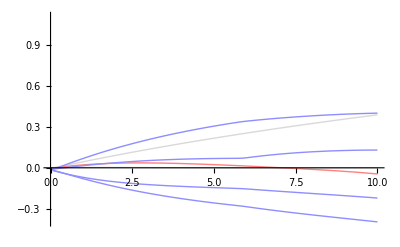

```mathematica
plotConfigurationData[data]
```